# Качающаяся машина Атвуда

-Graphics-
Качающаяся машина Атвуда = веревка с грузами разной массы на концах (отношение масс левого груза к правому = μ), перекинутая через два гвоздя ;

В этой программе...
Animation: показывает траекторию движения и анимирует движение на заданном временном отрезке;
PhasePortraitForR и PhasePortraitForθ: фазовый портрет для θ и r соответственно; 
EnergyCheck:показывает отношение изменения энергии системы (относительно начальной энергии) к начальной энергии;
При касании креплений радиальная скорость груза меняется на противоположную.

Уравнения, описывающие систему

-Graphics-

Piecewise[{{M g-T=M a=-M (d^2 r)/dt^2, (1)}, {m g cosθ - T = m a_r, (2)}, {-m g sinθ = ma_θ, (3)}}]

Piecewise[{{a_r= (d^2 r)/dt^2-(r(dθ/dt))^2, }, {a_θ=r(d^2 θ)/dt^2+2 dr/dt dθ/dt, }}]

Piecewise[{{m g cosθ - M g - M(d^2 r)/dt^2 = m ((d^2 r)/dt^2-(r(dθ/dt))^2), (2)-(1)}, {-m g sinθ = m (r(d^2 θ)/dt^2+2 dr/dt dθ/dt), (3)}}]

[ μ  = M/m ]

Итог:
Piecewise[{{(d^2 r)/dt^2(μ+1)=r (dθ/dt)^2+g(cosθ-μ), }, {-g sinθ= r (d^2 θ)/dt^2 + 2 dr/dt dθ/dt, }}]

Энергия:
E_p= - M g y - m g r cosθ
E_k=1/2 M (dy/dt)^2+1/2 m ((dr/dt)^2+(r^2(dθ/dt))^2)
E = E_p + E_k
ϵ  = E/m = 1/2 μ(dr/dt)^2+1/2((dr/dt)^2+r^2(dθ/dt)^2)+g r(μ-cosθ)

```mathematica
Animation[θ0n_,ω0n_,vr0n_,tEndn_,μn_]:=Module[{ω0=ω0n,vr0=vr0n,μ=μn,θ0=θ0n,tEnd=tEndn,t,soln,eqns,trajectory,pegs,rope,line,balls,r,θ},
eqns={r''[t] (μ+1)==r[t](θ'[t])^2+9.8(Cos[θ[t]]-μ), -9.8 Sin[θ[t]]==r [t]* θ''[t]+2 r'[t]* θ'[t],
θ[0]==θ0, r[0]==1,θ'[0]==ω0, r'[0]==vr0,
WhenEvent[r[t]==0,r'[t]->-r'[t]],WhenEvent[r[t]==2,r'[t]->-r'[t]]};
soln=NDSolve[eqns,{r,θ},{t,0,tEnd},MaxSteps->∞];
trajectory=ParametricPlot[Evaluate[{0.5+r[t]*Sin[θ[t]],-r[t]*Cos[θ[t]]}/.soln],{t,0,tEnd}];
Animate[
First[
{
pegs=Graphics[{Red,Disk[{-0.5,0},0.025],Red,Disk[{0.5,0},0.025]}];
rope=Graphics[{Thick,Gray,Line[{{-0.5,r[t]-2},{-0.5,0},{0.5,0},{0.5+r[t]*Sin[θ[t]],-r[t]*Cos[θ[t]]}}]}];
balls=Graphics[{Blue,Disk[{-0.5,r[t]-2},0.05],Disk[{0.5+r[t]*Sin[θ[t]],-r[t]*Cos[θ[t]]},0.05]}];
line=Graphics[{Black,Thick,Dashed,Line[{{-1.5,0},{1.5,0}}]}];

Show[{line,trajectory,rope,pegs,balls},PlotRange->{{-2,2},{0.5,-1.5}},ImageSize->Large]
}/.soln⟦1⟧],{{t,0,"t"},0,tEnd},Alignment->Center,AnimationRunning->False,AnimationRate->1,ControlPlacement->Bottom, AnimationRunTime->1, Bookmarks->{"start":>{t=0},"stop":>{t=10}}
]
]
PhasePortraitForR[θ0n_,ω0n_,vr0n_,tEndn_,μn_]:=Module[
{ω0=ω0n,vr0=vr0n,μ=μn,θ0=θ0n,tEnd=tEndn,t,soln,eqns,r,θ,Rpp},
eqns={r''[t] (μ+1)==r[t](θ'[t])^2+9.8(Cos[θ[t]]-μ), -9.8 Sin[θ[t]]==r [t]* θ''[t]+2 r'[t]* θ'[t],
θ[0]==θ0, r[0]==1  ,θ'[0]==ω0, r'[0]==vr0,
WhenEvent[r[t]==0,r'[t]->-r'[t]],WhenEvent[r[t]==2,r'[t]->-r'[t]]};
soln=NDSolve[eqns,{r,θ},{t,0,tEnd},MaxSteps->∞];
Rpp=ParametricPlot[Evaluate[{r[t],r'[t]}/.soln],{t,0,tEnd},AspectRatio->1/GoldenRatio,PlotRange->All, PlotTheme->"Scientific", ImageSize->Large, PlotLabel->Style["Phase portrait for R",FontSize->14, FontFamily->"Verdana", FontWeight->Bold]]
]
PhasePortraitForθ[θ0n_,ω0n_,vr0n_,tEndn_,μn_]:=Module[
{ω0=ω0n,vr0=vr0n,μ=μn,θ0=θ0n,tEnd=tEndn,t,soln,eqns,r,θ,θpp},
eqns={r''[t] (μ+1)==r[t](θ'[t])^2+9.8(Cos[θ[t]]-μ), -9.8 Sin[θ[t]]==r [t]* θ''[t]+2 r'[t]* θ'[t],
θ[0]==θ0, r[0]==1 ,θ'[0]==ω0, r'[0]==vr0,
WhenEvent[r[t]==0,r'[t]->-r'[t]],WhenEvent[r[t]==2,r'[t]->-r'[t]]};
soln=NDSolve[eqns,{r,θ},{t,0,tEnd},MaxSteps->∞];
θpp=ParametricPlot[Evaluate[{θ[t],θ'[t]}/.soln],{t,0,tEnd},AspectRatio->1/GoldenRatio,PlotRange->All, PlotTheme->"Scientific", ImageSize->Large, PlotLabel->Style["Phase portrait for θ",FontSize->14, FontFamily->"Verdana", FontWeight->Bold]]
]
EnergyCheck[θ0n_,ω0n_,vr0n_,tEndn_,μn_]:=Module[
{ω0=ω0n,vr0=vr0n,μ=μn,θ0=θ0n,tEnd=tEndn,t,soln,eqns,r,θ,ϵ,ϵ0},
eqns={r''[t] (μ+1)==r[t](θ'[t])^2+9.8(Cos[θ[t]]-μ), -9.8 Sin[θ[t]]==r [t]* θ''[t]+2 r'[t]* θ'[t],
θ[0]==θ0, r[0]==1  ,θ'[0]==ω0, r'[0]==vr0,
WhenEvent[r[t]==0,r'[t]->-r'[t]],WhenEvent[r[t]==2,r'[t]->-r'[t]]};
soln=NDSolve[eqns,{r,θ},{t,0,tEnd},MaxSteps->∞];
ϵ[t_]:=1/2 μ(D[r[t],t])^2+1/2((D[r[t],t])^2+(r[t])^2(D[θ[t],t])^2)+9.8 r[t](μ-Cos[θ[t]]);
ϵ0=1/2 μ(vr0)^2+1/2((vr0)^2+(ω0)^2)+9.8 (μ-Cos[θ0]);
Plot[Evaluate[{(ϵ[t]-ϵ0)/ϵ0}/.soln],{t,0,tEnd},PlotRange->All, PlotTheme->"Scientific", ImageSize->Large, PlotLabel->Style["Energy conservation check",FontSize->14, FontFamily->"Verdana", FontWeight->Bold]]
]
```

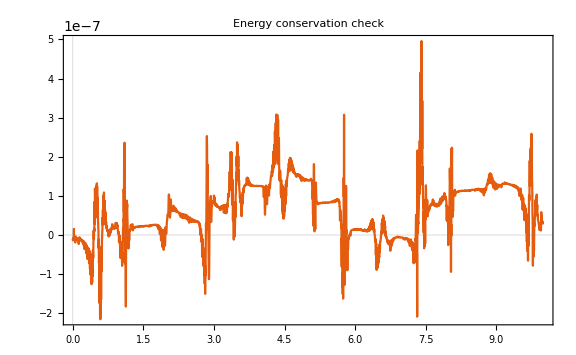

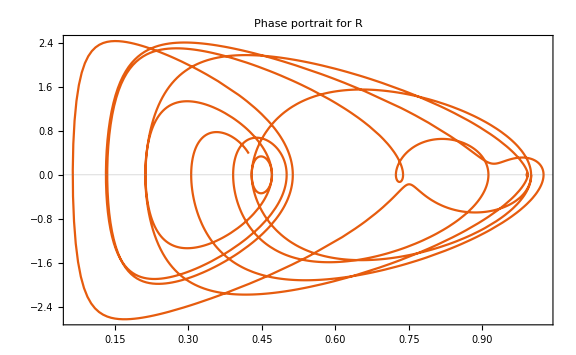

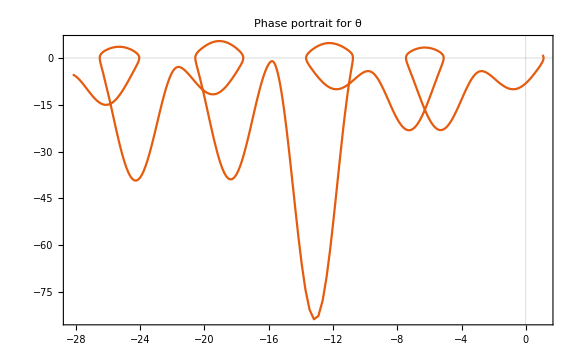

```mathematica
values={π/3,1,0,10,2};
animation = Animation[values[[1]],values[[2]],values[[3]],values[[4]],values[[5]]]
EnergyCheck[values[[1]],values[[2]],values[[3]],values[[4]],values[[5]]]
PhasePortraitForR[values[[1]],values[[2]],values[[3]],values[[4]],values[[5]]]
PhasePortraitForθ[values[[1]],values[[2]],values[[3]],values[[4]],values[[5]]]
```

```mathematica
Export["atwood_animation.gif",animation, "AnimationDuration"->10, "FrameRate"->10]
```

atwood_animation.gif

```mathematica
Manipulate[

Module[{ω0=ω0n,vr0=vr0n,μ=μn,θ0=θ0n,tEnd=tEndn,t,soln,eqns,trajectory,pegs,rope,line,balls,r,θ},
eqns={r''[t] (μ+1)==r[t](θ'[t])^2+9.8(Cos[θ[t]]-μ), -9.8 Sin[θ[t]]==r [t]* θ''[t]+2 r'[t]* θ'[t],
θ[0]==θ0, r[0]==1 ,θ'[0]==ω0, r'[0]==vr0,
WhenEvent[r[t]==0,r'[t]->-r'[t]],WhenEvent[r[t]==2,r'[t]->-r'[t]]};
soln=NDSolve[eqns,{r,θ},{t,0,tEnd},MaxSteps->∞];
trajectory=ParametricPlot[Evaluate[{0.5+r[t]*Sin[θ[t]],-r[t]*Cos[θ[t]]}/.soln],{t,0,tEnd},PlotRange->{{-1,2},{-2,1}},ImageSize->Large,PlotPoints->1000]
],{{ω0n,0,"Нач. угловая скорость"},0,1,Appearance->"Open",Appearance->"Labeled"},{{vr0n,0,"Нач. радиальная скорость"},0,2,Appearance->"Open",Appearance->"Labeled"},{{μn,10,"Отношение масс"},0,15,Appearance->"Open",Appearance->"Labeled"},{{θ0n,1/4 π,"Начальный угол"},0,1/2 π,Appearance->"Open",Appearance->"Labeled"},{{tEndn,2,"Время"},0.1,20,Appearance->"Open",Appearance->"Labeled"},ControlPlacement->Left
]
```